```mathematica
r=1;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

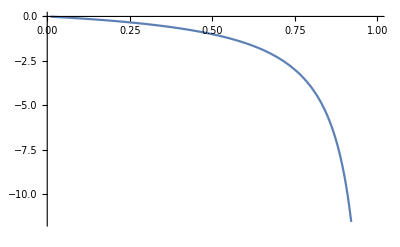
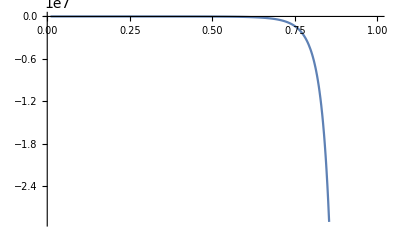
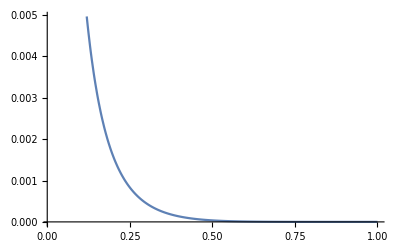
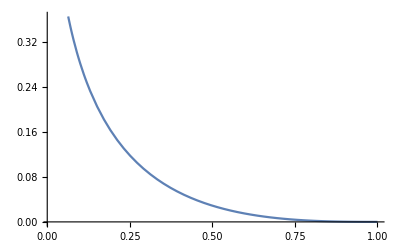
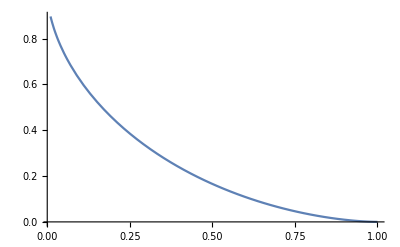
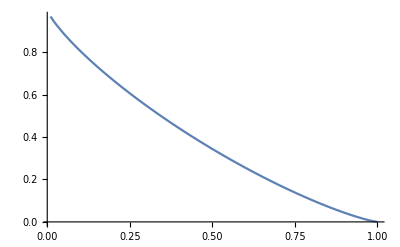
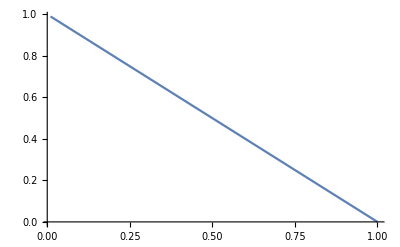
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[(r^i - x^i)^(1/i),{x,0.01,r}],{i,-1, 1, .2}]
```

```mathematica
r=1
areas = Table[Integrate[(r^p - x^p)^(1/p), {x, 0, r}],{p,.6,1.4, .2}]
```

1

```mathematica
Integrate[(d^k - x^k)^(1/k), x]
```

x (d^k-x^k)^(1/k) (1-d^-k x^k)^(-1/k) Hypergeometric2F1[-1/k,1/k,1+1/k,d^-k x^k]

```mathematica
Table[Plot[Integrate[(r^p - x^p)^(1/p), {x, 0, p}],{r, 0.6, 1.4}],{p,.6,1.4, .2}]
```

```mathematica
p=.9;
Plot[Integrate[(r^p - x^p)^(1/p), {x, 0, p}],{r, 0.6, 1.4}]
```

0.9

```mathematica
Clear[r]
i= 0.6;
Table[Integrate[(r^i - x^i)^(1/i),{x,0,r}], {r, 1, }]
```

```mathematica
N[(√π Gamma[4/3])/(2^(2/3) Gamma[5/6])]
```

0.883319

```mathematica
p= .6;
```

```mathematica
r=1.4;
Integrate[(r^p - x^p)^(1/p),{x,0,r}]
```

0.479124

```mathematica
Table[Integrate[(1 - x^p)^(1/p),{x,0,1}], {p, 0.1, 2, 0.01} ]
```

{5.41254×10^-6,0.0000182211,0.0000499262,0.000116795,0.000241366,0.000451785,0.000780399,0.00126194,0.00193161,0.00282332,0.00396825,0.00539377,0.00712273,0.00917313,0.011558,0.0142857,0.01736,0.0207805,0.0245433,0.0286415,0.0330654,0.0378032,0.0428413,0.0481648,0.0537579,0.0596041,0.0656865,0.0719881,0.0784918,0.0851809,0.0920388,0.0990496,0.106198,0.113468,0.120846,0.128319,0.135873,0.143496,0.151177,0.158904,0.166667,0.174456,0.182263,0.190079,0.197896,0.205707,0.213505,0.221284,0.229038,0.236762,0.244451,0.252101,0.259707,0.267265,0.274773,0.282227,0.289625,0.296964,0.304241,0.311455,0.318605,0.325687,0.332702,0.339648,0.346523,0.353328,0.360061,0.366721,0.373309,0.379824,0.386266,0.392634,0.398928,0.40515,0.411298,0.417373,0.423375,0.429304,0.435161,0.440947,0.446661,0.452304,0.457877,0.46338,0.468814,0.474179,0.479476,0.484707,0.48987,0.494968,0.5,0.504968,0.509872,0.514713,0.519492,0.524209,0.528866,0.533462,0.537999,0.542478,0.546899,0.551262,0.55557,0.559822,0.56402,0.568163,0.572253,0.57629,0.580276,0.584211,0.588095,0.59193,0.595715,0.599453,0.603143,0.606786,0.610382,0.613934,0.61744,0.620902,0.624321,0.627697,0.63103,0.634322,0.637572,0.640783,0.643953,0.647084,0.650176,0.65323,0.656247,0.659226,0.662169,0.665076,0.667948,0.670785,0.673587,0.676356,0.679091,0.681793,0.684463,0.687101,0.689708,0.692284,0.694829,0.697344,0.699829,0.702285,0.704712,0.707111,0.709482,0.711826,0.714142,0.716431,0.718694,0.720931,0.723143,0.725329,0.727491,0.729627,0.73174,0.733829,0.735894,0.737936,0.739955,0.741952,0.743927,0.745879,0.74781,0.74972,0.751609,0.753477,0.755325,0.757153,0.75896,0.760749,0.762518,0.764267,0.765999,0.767711,0.769406,0.771082,0.772741,0.774382,0.776005,0.777612,0.779202,0.780776,0.782332,0.783873,0.785398}

```mathematica
Table[Integrate[(1 - x^p)^(1/p),{x,0,1}], {p, 2, 5, 0.1} ]
```

{0.785398,0.799815,0.812852,0.824675,0.835428,0.845234,0.854198,0.862414,0.869961,0.876909,0.883319,0.889245,0.894734,0.899827,0.904562,0.90897,0.913082,0.916922,0.920515,0.92388,0.927037,0.930003,0.932792,0.935418,0.937893,0.94023,0.942437,0.944524,0.946501,0.948374,0.95015}

```mathematica
N[%, 4]
```

{ConditionalExpression[(1. (-1.+r^0.5)^2. (0.5 r^0.5-1.33333 r^1.+r^1.5))/((1.-1./r^0.5)^2. r^1.5), Re[r^0.5]>1.&&Re[1/r^0.5]<1.],(1. (-1.+r^0.55)^1.81818 Hypergeometric2F1[-1.81818,1.81818,2.81818,1./r^0.55])/((1.-1./r^0.55)^1.81818),(1. (-1.+r^0.6)^1.66667 Hypergeometric2F1[-1.66667,1.66667,2.66667,1./r^0.6])/((1.-1./r^0.6)^1.66667),(1. (-1.+r^0.65)^1.53846 Hypergeometric2F1[-1.53846,1.53846,2.53846,1./r^0.65])/((1.-1./r^0.65)^1.53846),(1. (-1.+r^0.7)^1.42857 Hypergeometric2F1[-1.42857,1.42857,2.42857,1./r^0.7])/((1.-1./r^0.7)^1.42857),ConditionalExpression[(1. (-1.+r^0.75)^1.33333 Hypergeometric2F1[-1.33333,1.33333,2.33333,1./r^0.75])/((1.-1./r^0.75)^1.33333), ],(1. (-1.+r^0.8)^1.25 Hypergeometric2F1[-1.25,1.25,2.25,1./r^0.8])/((1.-1./r^0.8)^1.25),(1. (-1.+r^0.85)^1.17647 Hypergeometric2F1[-1.17647,1.17647,2.17647,1./r^0.85])/((1.-1./r^0.85)^1.17647),(1. (-1.+r^0.9)^1.11111 Hypergeometric2F1[-1.11111,1.11111,2.11111,1./r^0.9])/((1.-1./r^0.9)^1.11111),(1. (-1.+r^0.95)^1.05263 Hypergeometric2F1[-1.05263,1.05263,2.05263,1./r^0.95])/((1.-1./r^0.95)^1.05263),ConditionalExpression[(1. (-1.+r^1.)^1. (-0.5+r^1.))/((1.-1./r^1.)^1. r^1.), Re[r^1.]>1.||Re[r^1.]<0||r^1.∉ℝ],(1. (-1.+r^1.05)^0.952381 Hypergeometric2F1[-0.952381,0.952381,1.95238,1./r^1.05])/((1.-1./r^1.05)^0.952381),(1. (-1.+r^1.1)^0.909091 Hypergeometric2F1[-0.909091,0.909091,1.90909,1./r^1.1])/((1.-1./r^1.1)^0.909091),(1. (-1.+r^1.15)^0.869565 Hypergeometric2F1[-0.869565,0.869565,1.86957,1./r^1.15])/((1.-1./r^1.15)^0.869565),(1. (-1.+r^1.2)^0.833333 Hypergeometric2F1[-0.833333,0.833333,1.83333,1./r^1.2])/((1.-1./r^1.2)^0.833333),ConditionalExpression[(1. (-1.+r^1.25)^0.8 Hypergeometric2F1[-0.8,0.8,1.8,1./r^1.25])/((1.-1./r^1.25)^0.8), ],(1. (-1.+r^1.3)^0.769231 Hypergeometric2F1[-0.769231,0.769231,1.76923,1./r^1.3])/((1.-1./r^1.3)^0.769231),(1. (-1.+r^1.35)^0.740741 Hypergeometric2F1[-0.740741,0.740741,1.74074,1./r^1.35])/((1.-1./r^1.35)^0.740741),(1. (-1.+r^1.4)^0.714286 Hypergeometric2F1[-0.714286,0.714286,1.71429,1./r^1.4])/((1.-1./r^1.4)^0.714286),(1. (-1.+r^1.45)^0.689655 Hypergeometric2F1[-0.689655,0.689655,1.68966,1./r^1.45])/((1.-1./r^1.45)^0.689655),ConditionalExpression[(1. (-1.+r^1.5)^0.666667 Hypergeometric2F1[-0.666667,0.666667,1.66667,1./r^1.5])/((1.-1./r^1.5)^0.666667), ]}

```mathematica
Evaluate[(0.99999999999999 (-0.9999999999999946+r^0.55)^1.8181818181818181 Hypergeometric2F1[-1.8181818181818181,1.8181818181818181,2.8181818181818183,0.9999999999999946/r^0.55])/(1.-0.9999999999999946/r^0.55)^1.8181818181818181]
```

(1. (-1.+r^0.55)^1.81818 Hypergeometric2F1[-1.81818,1.81818,2.81818,1./r^0.55])/((1.-1./r^0.55)^1.81818)

```mathematica
Table[p, {p, 0.1, 2, 0.01} ]
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.}

```mathematica
For[p=0.4, p≤2.4, p += .4, Plot[(1 - x^p)^(1/p),{x,0,1}]](*, {p, 0.1, 2, 0.01}]*)
```

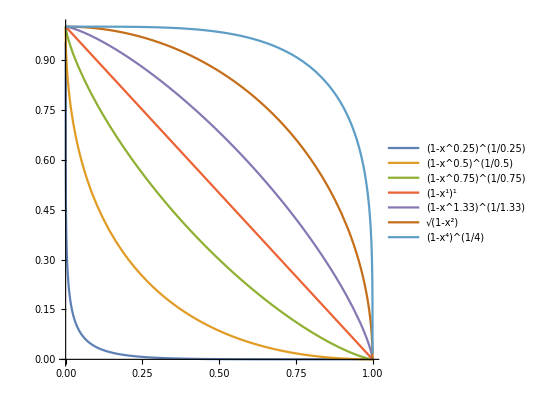

```mathematica
p1 = Plot[{(1 - x^.25)^(1/.25),(1 - x^.5)^(1/.5),(1 - x^.75)^(1/.75),(1 - x^1)^(1),(1 - x^1.33)^(1/1.33),(1 - x^2)^(1/2),(1 - x^4)^(1/4)},{x,0,1},PlotLegends->"Expressions", AspectRatio->1]
```

```mathematica
Export["exportP1.pdf",p1]
```

exportP1.pdf

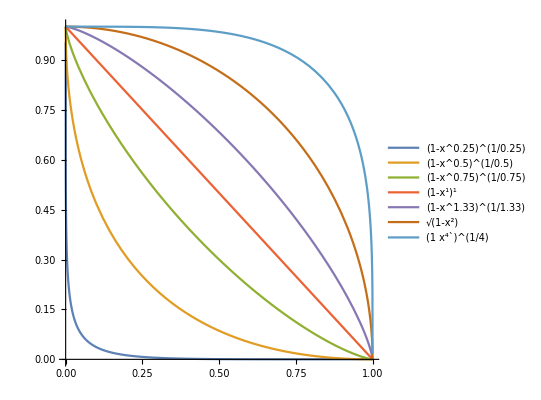

```mathematica
Save[%, 'here.pdf']
```

Save::argmu: Save called with 1 argument; 2 or more arguments are expected.

Save[-Graphics-]